# Implement Petri Net

Pumeng Lyu

Jofre Espigule-Pons

In my project, I am going to write a package to visualize a mathematical modeling language for the description of distributed systems called Petri net. Petri net is a set of discrete event dynamic system. Let’s further explore the usefulness of Petri net and how I try to visualize and make analysis on it step by step.

## What consists of a Petri net?

A Petri net includes places, transitions and arcs. Arcs must go from a place to a transition or vice versa, which makes a Petri net a directed bipartite graph and the nodes represent transitions (events that may occur to cause change in states, marked by square) and places (conditions, marked by circles). These conditions make our first group of functions to check if the input structure is a Petri net, with the function named petriNetQ.

petriNetQ [ Places, Transitions, Arcs ]: returns True if the input satisfy the requirement to build a Petri net, else returns False.
Helper function: 
applyBooleanToList[ Logic operator, List of conditions ]: it is a helper function to apply boo-lean operator on a list of conditions. We are going to use this 				function to check if for the input data to build Petri net, the places list has no common vertex with the transition list, and also check if the graph is 			bipartite.
Input: 	<|"States" -> list1, "Transitions" -> list2,  "Arcs" -> list3|>
Return: 	True or False

```mathematica
applyBooleanToList[logic_, booleanList_]:= 
	Fold[logic, First @ booleanList, Rest @ booleanList]
```

```mathematica
petriNetQ[<|"States"-> s__,"Transitions"-> t__, "Arcs"-> a__|>]:= Module[{g},
	g = Graph[DirectedEdge @@@ a];
	applyBooleanToList[And, 
		{Intersection[s,t] == {}, 
		BipartiteGraphQ[g]}]
]
```

Here is an example of petriNetQ. The input in this case satisfy the condition for making a petriNet.

```mathematica
ClearAll[graph];
graph =petriNetQ[<|"States"->{a,b,c,d,e,f,g,h},"Transitions"->{t1,t2,t3,t4,t5,t6}, "Arcs"-> List @@@{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}|>]
```

True

But what is the Petri net looks like? Here we need a function to visualize Petri net with the help of Graph function. First we need to make a petriNetData function close to the OceanData function already in the wolfram language repository.

petriNetData returns the graph visualization of the petri net in a graph form, if the input satisfy the Petri net structure.
petriNetData [Places, Transitions, Arcs]:
Input: 	<|"States" -> list1, "Transitions" -> list2,  "Arcs" -> list3|>
Return: 	If the input is a valid Petri Net, it returns a data list includes graph, with its places, transitions and arcs; if the input is not a valid Petri net, it will tag 			Failed.

```mathematica
petriNetData[<|"States"->s__,"Transitions"->t__, "Arcs"-> a__|>] := If[petriNetQ[<|"States"->s,"Transitions"->t, "Arcs"-> a|>], 
	{Graph[Join[s,t], DirectedEdge @@@ a, VertexShapeFunction -> Join[Thread[s->"Circle"],Thread[t-> "Square"]],
	VertexLabels->"Name", VertexStyle-> Join[Thread[s -> LightBlue],Thread[t -> LightGray]], VertexSize->Large], 
	s,t,DirectedEdge @@@ a}, $Failed; Print["Fail!"]]
```

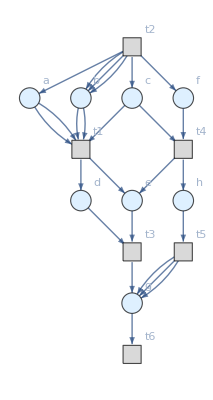
{-Graphics-,{a,b,c,d,e,f,g,h},{t1,t2,t3,t4,t5,t6},{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}}

```mathematica
ClearAll[graph];
graph =petriNetData[<|"States"->{a,b,c,d,e,f,g,h},"Transitions"->{t1,t2,t3,t4,t5,t6}, "Arcs"-> List @@@{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}|>]
```

A Petri net includes places, transitions and arcs. Arcs must go from a place to a transition or vice versa, which makes a Petri net a directed bipartite graph and the nodes represent transitions (events that may occur to cause change in states, marked by square) and places (conditions, marked by circles).

Also we need another thing in Petri net: tokens. The tokens describe the current state in each places, and the number of the tokens determine the firing option to the next state, as we will explain in detail later. Now we can add text-dot to show the tokens and visualize the Petri net as its initial state.

petriNetInit [Petri net net, List of initial conditions]: 
Input: 	Petri net structure net, a List defining the initial conditions of the graph.
Return: 	A graph with places(circles), transitions(squares), arcs, tokens on places.

Helper function:
textDot[vertex, n, coordinateDictionary]: build string of n dots on specific location on the graph.
buildDotsList[coordinateDictionary, vertextWeightDictionary, List of vertices]: add dots on each places’ vertex depending on the vertex weight.

```mathematica
textDot[vertex_, n_, coordinatesDict_]:= Text[StringRepeat["•", n], coordinatesDict[vertex]]
```

```mathematica
buildDotsList[coordinateDict_, vertexWeightDict_, vertices_]:= Module[
	{res = {}},
	Scan[AppendTo[res,textDot[#, vertexWeightDict[#], coordinateDict]]&, vertices];
	res
]
```

```mathematica
petriNetInit[pnet_,init_]:= Module[
	{g, coordinatesDict, vertexWeightDict, graphData, vertexWeight, vertexWeightsDict, epilog},
	g = Graph[First @ pnet, VertexWeight -> Join[Thread[Part[pnet,2] -> init], Thread[Part[pnet,3] -> 0]]];
	graphData = ToExpression @ StringReplace[(ToString[FullForm[g]]), "Graph" -> "List"];
	vertexWeight = Last @ (Last @ graphData[[3]]);
	coordinatesDict = Association @ Thread[graphData[[1]] -> VertexCoordinates /. AbsoluteOptions[g, VertexCoordinates]];
	vertexWeightsDict = Association @ Thread[graphData[[1]] -> vertexWeight];
	epilog = buildDotsList[coordinatesDict, vertexWeightsDict, graphData[[1]]];
	Graph[g, Epilog -> epilog]
]
```

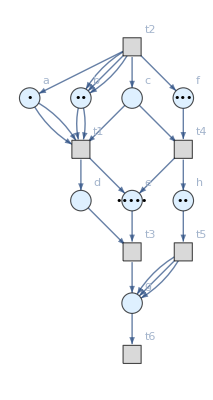

```mathematica
petriNetInit[graph,{1,2,0,0,5,3,0,2}]
```

Now we can clearly see what a Petri net is. These blue circles: a, b, c, d, e, f, g, some with dots(tokens) are places; these gray squares: t1, t2, t3, t4, t5, t6 are transitions; and the edges connected between places and transitions are arcs.

## Codes for Petri net visualization

The next step is to make our Petri net “running”. To do this we need the rules for “firing”. Firing means the tokens from source places with a transition move to source states based on the number of edges between nodes. For example, as the Petri net showed above, place a now has 1 token, and the number of edges between a and t1 is 2, which means place a needs to consume 2 tokens to set up transition t1. The system will randomly select one transition that meets the requirement to fire. For example, if the condition to start transition t1, as t1 has 1 edge to d, and one edge to g, so it will pass 1 token to place d and 1 token to place g. Now we write codes to achieve these firing rules.

petriNetRun[A Petri net data structure, initial number of tokens in each places, steps need to visualize]
Input: 	A Petri net and number of tokens in each places, and the steps that the user wants to run.
Return: 	Dynamic visualization of how tokens move from state to state in the first n steps.

In order to make our Petri net running, we need some helper functions:
checkFiring[ A Petri net data structure, transitions, current number of tokens in each places ]:  
	check if this specific transition meets the requirement to fire.
makeFiring[ A Petri net data structure, transitions, current number of tokens in each places ]:  
	Randomly choose one of the available transitions to fire, reduce the tokens from the source states.
updateFiring[ A Petri net data structure, transitions, current number of tokens in each places ]:
	 update the tokens of sink states of the transitions and finish current step of firing.

```mathematica
checkFiring[pnet_, transition_, current_]:= Module[
	{tokenList},
	tokenList = Length@EdgeList[First@pnet, # -> transition] &/@ Part[pnet, 2];
	AllTrue[current - tokenList, NonNegative]
]
```

```mathematica
makeFiring[pnet_, transition_, current_]:= Module[
	{tokenDeleteList,tokenAddList},
	tokenDeleteList = Length@EdgeList[First@pnet, #->transition] &/@ Part[pnet,2];
	tokenAddList = Length@EdgeList[First@pnet, transition->#] &/@ Part[pnet,2];
	current - tokenDeleteList + tokenAddList
]
```

```mathematica
updateFiring[pnet_][current_]:= Module[
	{index},
	index = First @ RandomChoice[Position[checkFiring[pnet, #, current] &/@ pnet[[3]], True]];
	If[IntegerQ[index], 
	makeFiring[pnet, pnet[[3,index]], current], 
	Print["Dead!"]; Abort[]]
]
```

```mathematica
ClearAll[petriNetRun];
petriNetRun[pnet_, init_, step_Integer]:= Module[
	{current = init, g, index},
	current = Nest[updateFiring[pnet], current, step-1];
	index = First @ RandomChoice[Position[checkFiring[pnet, #, current] &/@ pnet[[3]], True]];
	If[IntegerQ[index], 
		makeFiring[pnet, pnet[[3,index]], current], 
		Print["Dead!"]; Abort[]];
	g = petriNetInit[pnet, current];
	HighlightGraph[g, {pnet[[3,index]]}]
]
```

We thus get the animation of the graph we displayed above in fifteen steps.

```mathematica
ListAnimate[Table[petriNetRun[graph,{1,2,0,0,5,3,0,2},n],{n,15}],SaveDefinitions->True]
```

## User interface and animation

A Petri net requires places, transitions, arcs, tokens and firing rules. It requires a lot of input for the users, which is not convenient. To make user input data for a Petri net easier, we are going to create a user interface and the program will translate the input from users to be a PetriNetData structure. Here is the code to start the user interface and helper functions to translate the input to be a Petri net data.

PetriNetGeneral[]: start a user interface and translate user input into a Petri net data structure. 
To achieve this, we need some helper function to interpret the user input:
makeMultipleEdges[<|”from”->source places,”to”->sink places,”numbers”->numbers of edges needed|>]: return a list of edges in the Petri net.
inputTranslator[<|”Places” -> List of places, “Transitions” -> List of transitions, “Arcs” -> List of arcs, 
	“Initial States”-> <|”e.g: 0,0,1”->initial number of tokens in each places|>, “Steps”-><|”Input the steps you want to animate”->number of steps 		want to visualize|>|>]: translate the user input to a data same as the structure of Petri net data.
makePetriNetFromInput[ A Petri net data structure ]: generate a visualization or animation of the Petri net step to step.

```mathematica
ClearAll[makeMultipleEdges];
makeMultipleEdges[<|"from"->in_,"to"->out_,"numbers"->num_|>]:= Module[{l={}},
	For[i=1,i<=num,i++, AppendTo[l,{in,out}]]; 
	l
]
```

```mathematica
ClearAll[inputTranslator];
inputTranslator[<|"Places" -> placeList_, "Transitions" -> transitionList_, "Arcs" -> arcList_, 
"Initial States"-> <|"e.g: 0,0,1"->init_|>, "Steps"-><|"Input the steps you want to animate"-> steps_|>|>]:=Module[
	{initialState},
	initialState = ToExpression /@ StringSplit[init,","];
	{<|"States"-> First /@ Values /@ placeList, 
	"Transitions"-> First/@ Values /@ transitionList,
	"Arcs"->Join @@ makeMultipleEdges /@ arcList|>, initialState, steps}
]
```

```mathematica
ClearAll[makePetriNetFromInput];
makePetriNetFromInput[input_]:= Module[
	{inputPnetData, initState, steps, pnet},
	{inputPnetData, initState, steps} = inputTranslator[input];
	pnet = petriNetData[inputPnetData];
	ListAnimate[Table[petriNetRun[pnet,initState, n],{n, steps}], AnimationRate->1.5,SaveDefinitions->True]
]
```

```mathematica
ClearAll[PetriNetGeneral];
PetriNetGeneral[]:= FormFunction[<|"Places" -> RepeatingElement[
	CompoundElement[<|"Circles"-> "String"|>]],"Transitions" -> RepeatingElement[CompoundElement[<|"Squares"-> "String"|>]],
	"Arcs" -> RepeatingElement[CompoundElement[<|"from"-> "String","to"-> "String","numbers"-> "Integer"->1|>]],
	"Initial States" -> CompoundElement[{"e.g: 0,0,1"->"String"}],
	"Steps" -> CompoundElement[{"Input the steps you want to animate"-> "Integer"->5}]|>, makePetriNetFromInput][]
```

So when we start the function PetriNetGeneral[], the program will pop out a menu to ask users to input places, transitions, arcs, initial state and steps they want to animate. Below is an example of the user’s interface and the animation after we click “submit” button.

```mathematica
SetDirectory["/Users/luzhiryou/Documents/GitHub/WSS-2019/Final Project"];
Import["GenInterface.jpg"]
```

-Graphics-

```mathematica
PetriNetGeneral[]
```

A more user-friendly might come as future work, but this version will definitely save out time to input data to make and visualize a Petri net.

## Petri net application in chemistry

Some papers indicate that Petri nets were first invented in 1939 by Carl Adam Petri for the purpose of describing chemical reactions. To help those interested in chemical reactions, we write another function to visualize the chemical reactions using Petri net.
To interpret a chemical reactions into a Petri net, we need series of helper functions: reduceParentheses, getChemicals, getStoichemstry, inputTranslatorHelper. Then with the help from Wolfram Alpha repository, we are able to translate the input into a Petri net data structure.

```mathematica
ClearAll[reduceParentheses];
reduceParentheses[st_String]:= Module[
	{s},
	If[StringPart[st,1] ==="(", s = StringDrop[st,1], s = st];
	If[StringPart[s,-1] ===")", s = StringDrop[s,-1], s];
	s
]
```

```mathematica
getChemicals[st_String]:= First @ StringCases[st, "[" ~~Shortest[c__]~~"]"->c]
```

```mathematica
ClearAll[getStoichiometry];
getStoichiometry[st_String]:=If[StringContainsQ[st,"^"],ToExpression@First@StringCases[st, "^" ~~number__ ->number],1]
```

```mathematica
ClearAll[inputTranslatorHelper];
inputTranslatorHelper[list_List]:= List @@@ Thread[getChemicals/@list-> getStoichiometry/@list]
```

With the help of Wolfram Data Repository, we define the function waChemicalReaction to fetch the reaction and return Petri net stucture.
waChemicalReaction [ Chemical Reaction equations ]: returns a Petri net and its initial conditions.

```mathematica
ClearAll[waChemicalReaction];
waChemicalReaction[chemicalReaction_String]:= Module[
	{s,string},
	s = WolframAlpha[chemicalReaction,{{"ReactionKineticsConstant:ChemicalReactionData",1},"ComputableData"}];
	If[s === Missing["NotAvailable"], Print["Missing, try a different notation."]; Abort[],
	s = StringDrop[s, StringLength["K_c  =  "]];
	s = StringSplit[s, "/"];
	s = reduceParentheses/@ s;
	s = StringSplit[s," "];
	string = getChemicals/@Flatten @ s;
	s = inputTranslatorHelper /@ s;
	{s, string}]
]
```

```mathematica
ClearAll[getPlaces];
getPlaces[Chem_List]:= Association /@ Thread["Circles" -> Chem]
```

```mathematica
ClearAll[getTransitions];
getTransitions[{leftChem_List,rightChem_List}] := {<|"Squares"->"T1"|>}
```

```mathematica
ClearAll[getArcs];
getArcs[{leftChems_List, rightChem_List}]:= Module[
	{left, right},
	left = Join @@ Map[{<|"from"-> "T1","to"-> #[[1]],"numbers"-> #[[2]]|>}&, leftChems];
	right = Join @@ Map[{<|"from"-> #[[1]],"to"-> "T1","numbers"-> #[[2]]|>}&, rightChem];
	Join @@ {left, right}
]
```

```mathematica
buildPetriNet[reactions_, chemicals_, init_, steps_]:= Module[
	{places, trans, arcs},
	places = getPlaces[chemicals];
	trans = getTransitions[reactions];
	arcs = getArcs[reactions];
	<|"Places"-> places, "Transitions"->trans, "Arcs"->arcs, "Initial States"-><|"e.g: 0,0,1"->init|>,"Steps"-><|"Input the steps you want to animate"->steps|>|>
]
```

```mathematica
TranslateFromChemToGeneral[<|"Reactions"->{<|"Input the reactions"->st_|>},
	"Initial States"-><|"e.g: 0,0,1"->init_|>,
	"Steps"-><|"Input the steps you want to animate"->steps_|>|>]:= Module[
	{reactants, chemicals,input, inputPnetData, pnet},
	{reactants, chemicals} = waChemicalReaction[st];
	input = buildPetriNet[reactants, chemicals, init, steps];
	makePetriNetFromInput[input]
]
```

```mathematica
ClearAll[PetriNetChemistry];
PetriNetChemistry[]:= FormFunction[<|"Reactions" -> RepeatingElement[CompoundElement[<|"Input the reactions"-> "String"|>]],
	"Initial States" -> CompoundElement[{"e.g: 0,0,1"->"String"}],
	"Steps" -> CompoundElement[{"Input the steps you want to animate"-> "Integer"->5}]|>,TranslateFromChemToGeneral][]
```

Below is an example of visualizing a chemical reaction with input and output.

```mathematica
SetDirectory["/Users/luzhiryou/Documents/GitHub/WSS-2019/Final Project"];
Import["ChemInterface.jpg"]
```

-Graphics-

```mathematica
PetriNetChemistry[]
```

## Further Application of Petri net

Petri net, as a mathematical modeling language, indeed is not limited to visualize chemical processes. In fact, any mathematics model can be somewhat expressed with Petri net. So here we write a new user interface to visualize the Petri Net. Different from the previous user interface for general input or chemical reactions, this time we build the system based on transitions and its rate. So our ultimate goal is to build Petri net to visualize system of transitions and use the Petri net to build groups of ordinary differential equations (ODE) and make plots for further mathematical analysis. Here we make the function PetriSystemAnalyzer and its helper function to visualize the system with many transitions.

```mathematica
ClearAll[petriNetInputTranslatorHelper];
petriNetInputTranslatorHelper[<|"Source States"->sources_,
"Source States Stoichiometry"->sourceRatio_, "Sink States"->sink_, "Sink States Stoichiometry"->sinkRatio_, 
"Transition name"->trans_,"reaction rate"->rate_|>]:=Module[
	{sourceStates, sinkStates},
	sourceStates = List @@@ Thread[StringSplit[sources,","]-> ToExpression @ StringSplit[sourceRatio, ","]];
	sinkStates = List @@@ Thread[StringSplit[sink,","]-> ToExpression @ StringSplit[sinkRatio, ","]];
	<|"Transition"->{trans,rate},"SourceStates"->sourceStates,"SinkStates"-> sinkStates|>
]
```

```mathematica
ClearAll[petriNetInputTranslator];
petriNetInputTranslator[<|"Transitions"-> List_|>]:= petriNetInputTranslatorHelper /@ List
```

```mathematica
ClearAll[PetriNetSystemInput];
PetriNetSystemInput[]:=FormFunction[<|"Transitions" -> RepeatingElement
	[CompoundElement[<|"Source States"-> "String",
	"Source States Stoichiometry"-> "String",
	"Sink States"-> "String", "Sink States Stoichiometry"-> "String",
	"Transition name"-> "String","reaction rate"-> "Integer"->1|>]]|>, PetriSystemAnalyzer][]
```

Here we make the function PetriSystemAnalyzer and its helper function to visualize the system with many transitions.
petriNetSystemAnalyzer <|”Source States”->sources_,
	“Source States Stoichiometry”->sourceRatio_, “Sink States”->sink_, “Sink States Stoichiometry”->sinkRatio_, 
	“Transition name”->trans_,”reaction rate”->rate_|>]
Input: list of transitions, including sink states, source states, stoichiometry, transition name, transition rate and initial state.
Output: a Petri net visualize the systems with many transitions.

```mathematica
ClearAll[makeEdges];
makeEdges[<|"Transition"->transition_,"SourceStates"->sourcePlaces_,"SinkStates"-> sinkPlaces_|>]:= Module[
	{sourceEdges,sinkEdges},
	sourceEdges = DirectedEdge[p[First@#],t[First@transition]] -> Last@#&/@sourcePlaces;
	sinkEdges = DirectedEdge[t[First@transition],p[First@#]] -> Last@#&/@sinkPlaces;
	Join[sourceEdges,sinkEdges]
]
```

```mathematica
ClearAll[vsf];
vsf[scale_][pos_,p[v_],size_]:= {Circle[pos,scale First@size],Inset[v,pos+8size]}
vsf[scale_][pos_,t[v_],size_]:= {{Transparent,Rectangle[pos- scale size,pos+scale size]},Inset[v,pos+8size]}
```

```mathematica
ClearAll[PetriSystemAnalyzer];
PetriSystemAnalyzer[input_]:=Module[
	{systemTransitions, edgeData, edgeList, edgeWeights},
	systemTransitions = petriNetInputTranslator[input];
	edgeData = Join@@makeEdges/@systemTransitions;
	{edgeList,edgeWeights}={Keys @ edgeData, Values @ edgeData};
	Graph[edgeList,VertexShapeFunction-> vsf[6],EdgeWeight->edgeWeights,EdgeLabels->"EdgeWeight"]
]
```

Below is the example for this system user interface and output Petri net given the input.

```mathematica
SetDirectory["/Users/luzhiryou/Documents/GitHub/WSS-2019/Final Project"];
Import["systemInterface.jpg"]
```

-Graphics-

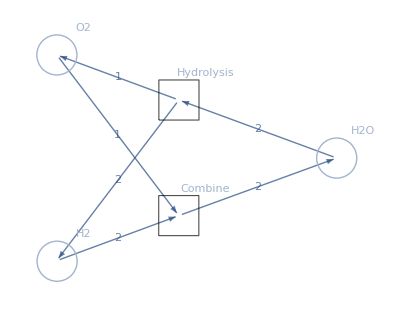

```mathematica
PetriNetSystemInput[]
```

As we said above, Petri net can be applied for many math models, population dynamics is one of the example. There are three transitions: birth, which inputs one rabbit and outputs two rabbits like asexual reproduction; predation, which converts rabbit plus wolf to two wolves, and death, which inputs one wolf and outputs nothing.

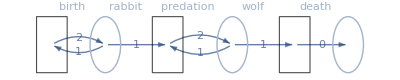

```mathematica
PetriNetSystemInput[]
```

With the Petri net structure visualized, we can input the structure, with the vertex weight of places interpreted as amount in current state, vertex weight of transitions interpreted as transition rate, we can build a system of ODEs and make a plot, which we will leave it for future effort.

Petri net can also be applied to deal with problems in physics and computer science. For example, deadlock is a topic with scheduling problems in operating systems. Below is an example of a deadlock Petri net. As in the case of reachability, we want to develop higher order tools to study if a given Petri net is deadlocked or not. With this, we might find easier to design scheduling mechanisms in our operating systems.

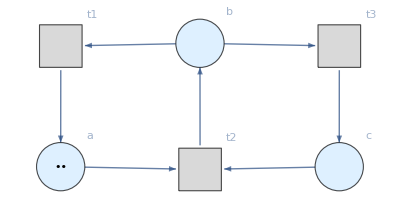

```mathematica
graph = petriNetData[<|"States"->{a,b,c},"Transitions"->{t1,t2,t3}, "Arcs"-> List @@@{t1->a, a-> t2, t2->b, b-> t1, c->t2, t3->c, b->t3}|>];
petriNetInit[graph,{2,0,0}]
```

## Discussion about mathematical properties of Petri net

Petri net, as a mathematical modeling language, indeed is not limited to visualize chemical processes. In fact, any mathematics model can be somewhat expressed with Petri net. However, from Wikipedia, papers written by John Baez, and StateBox archive, here are some open questions discussed with Petri net. 
The first problem is Reachability. According to Wikipedia, The reachability problem for Petri nets is to decide, given a Petri net N and a marking M, whether M can be reached from current state. This problem actually is not easy, and it was shown to be EXPSPACE-hard. But these days it turned out to be elementary. Here is a function named petriNetReachableQ.

petriNetReachableQ [ Neural Net n, init, Node m ]
Input: 	A Petri net named n, the initial condition of states, and the node marked as m we want to check.
Return: 	True if for Net n, m is reachable given the initial condition init in finite steps, else return False.

```mathematica
ClearAll[petriNetReachableQ];
petriNetReachableQ[pnet_, init_, place_]:= Module[
	{states, places, assoc},
	states = Total[NestList[updateFiring[pnet], init , 100]];
	places = First @ Rest @ pnet;
	assoc = Association[Thread[places -> states]];
	If[assoc[place] === 0, False, True]
]
```

```mathematica
petriNetReachableQ[graph,{1,2,0,0,5,3,0,2},c]
```

True

There are other properties remain discussed, such as boundedness and liveness. These are interesting graph properties we want to discuss here in Petri net.
For a place p in a Petri Net, it is k-bounded if it never contains more than k tokens in any reachable marking. For example, traffic light nets are bounded, since every places are 1-bounded, which means the system is in safe.

```mathematica
graph = petriNetData[<|"States"->{red1,green1,red2,green2,blue},"Transitions"->{t1,t2,t3,t4}, "Arcs"-> List @@@{t1->red1, red1-> t2, t2->green1, green1-> t1,t1->blue,blue->t2,t3->blue, blue->t4, t3->red2,red2->t4,t4->green2,green2->t3}|>];
ListAnimate[Table[petriNetRun[graph,{1,0,1,0,1},n],{n,10}],SaveDefinitions->True]
```

We thus write out a function to check the boundedness of a state given an initialized Petri net pnet.

kBoundedness[Petri net pnet, initial state, key p]:
Input: 	Petri net named pnet, initial state of the Petri net pnet and the state key we what to check
Return: 	an integer shows the boundedness of the state key.

```mathematica
kBoundedness[pnet_,init_][key_]:=Module[
	{states,length,assoc,index},
	length = Length[First @ Rest @pnet];
	assoc = Association[Thread[First @ Rest @ pnet -> Range[length]]];
	states = NestList[updateFiring[graph], init , 100];
	index =  assoc[key];
	Max[states[[All,index]]]
]
```

For example, we want to check the boundedness of the red light from the Petri net we created, which is 1.

```mathematica
kBoundedness[graph,{1,0,1,0,1}][red1]
```

1

On discussion of liveness in Petri net, there are four states in total. 
We will leave the discussion of  liveness and deadlock as future exploration.

## Author contact information

plyu122197@gmail.com